# Analog Elementary Cellular Automata

## Creating Cellular Automata that work on inputs in ℝ rather than in {0, 1}

## Description of Analog Automata

### Introduction to ECA

Conventional Wolfram Elementary Cellular Automata (ECA) are based on a set of rules repeatedly applied to each element of a row of cells. In the case of a neighbor distance of 1, ECA use a set of 8 rules which encode how an ECA should behave in each possible configuration of states of the cell and its immediate neighbors to the left and right. For example, in the following rule plot, the fourth rule describes that a cell should change it’s value to a 1 if itself and it’s neighbor to the right have a state of 0 and it’s neighbor to the left has a state of 1:

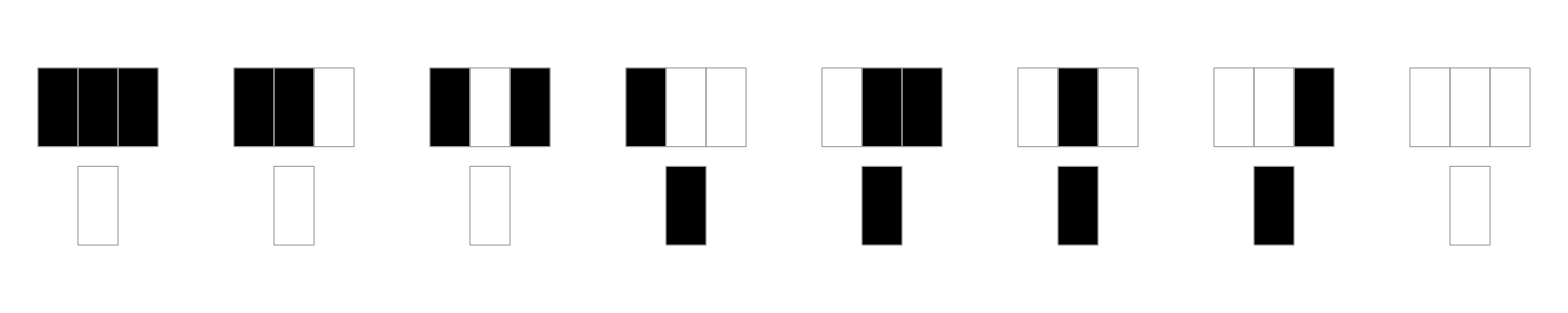

```mathematica
RulePlot[CellularAutomaton[30]]
```

### Writing Rules as Boolean Functions

The fourth rule can also be written in terms of a logical statement: if (x, y, z) corresponds to a cell’s immediate neighborhood, then the rule can be written as
r(x, y, z) = x ⋀ ~y ∧ ~z

In order to output a 1, x must be True, and y and z must be False, just as how in order for the fourth rule to apply, a cell’s neighborhood must be (1, 0, 0).

In fact, each of the rules can be written in this way:
    given a rule of the form
        (x_i, y_i, z_i) → N        (e.g. the fourth rule would be (1, 0, 0) → 1))
    then the rule can be written as
        r(x, y, z) = N ∧ (x == x_i) ∧ (y == y_i) ∧ (z == z_i)

### Writing Rule Sets as Boolean Functions

We can combine all of the rules in a set with OR operators, and so an entire rule set can be applied in a single boolean function. For example, here is the function describing the rule set for ECA[30]:

R(x, y, z) = (0 ∧ (x == 1) ∧ (y == 1) ∧ (z == 1)) ∨
                      (0 ∧ (x == 1) ∧ (y == 1) ∧ (z == 0)) ∨
                      (0 ∧ (x == 1) ∧ (y == 0) ∧ (z == 1)) ∨
                      (0 ∧ (x == 1) ∧ (y == 0) ∧ (z == 0)) ∨
                      (1 ∧ (x == 0) ∧ (y == 1) ∧ (z == 1)) ∨
                      (1 ∧ (x == 0) ∧ (y == 1) ∧ (z == 0)) ∨
                      (1 ∧ (x == 0) ∧ (y == 0) ∧ (z == 1)) ∨
                      (0 ∧ (x == 0) ∧ (y == 0) ∧ (z == 0))

Or in a more simplified form,

R(x, y, z) = (~x ∧ y ∧ z) ∨
                      (~x ∧ y ∧ ~z) ∨
                      (~x ∧ ~y ∧ z)

### Creating Analog Functions from Boolean Functions

This gives us a way to represent every possible set of rules as a binary function. Binary functions of this form can easily be transformed into analog functions that work for any inputs, not just binary inputs by replacing ~x operations with (1-x), x ∧ y with x * y, and x ∨ y with x + y.
(Note: x + y does not generally work as a replacement for x ∨ y, but in the case of rule sets where only one rule can be applied at a time, it doesn’t cause a problem.)

Applying these replacements, we get that:
R(x, y, z) = (1 - x) * y * z +
                      (1 - x) * y * (1 - z) +
                      (1 - x) * (1 - y) * z

By using this analog rule, cellular automata can be created that operate on all real numbers, and that exhibit some very interesting properties. By design, these analog cellular automata (ACA) behave the same as their boolean counterparts for inputs of 0 or 1, but they can also operate on any other real inputs.

### Interpretation

Another interpretation is to think of these analog functions as interpolating linearly between the rules in a rule set. For example, if you have a cell with a neighborhood of (1, 0, 0.5), then the updated state of the cell should be the average of the (1, 0, 0) rule and the (1, 0, 1) rule. This interpretation is how I originally described and derived these analog automata, and both this description and the description provided above are equivalent.

## Implementation

```mathematica
$MinPrecision = 2^-64;

(* All 3-tuples of 1 and 0, used for determining which rule to apply. Transposed so that each sublist corresponds to the inputs of x, y, and z, respectively. *)
transposedTuples = Transpose[Tuples[{0, 1}, 3]];

(* Given a rule vector (i.e., all the values of N, or the binary digits of a rule number), returns a function that implements it's analog analog *)
RuleFunction := Function[{ruleVector}, Function[{x, y, z}, 
Dot[
Reverse[
Times @@@ Transpose[((1 - transposedTuples)*(1 - {x, y, z})) + (transposedTuples * {x, y, z})]],
ruleVector
]]];

(* Creates a CA from a ruleVector. Mostly just used for convinience to not type out all the syntax to use a custom function for a CA. *)
CAfromVector[ruleVector_,initVal_:1,init_:101,t_:50] := 
CellularAutomaton[
{{p_, q_, r_}->(RuleFunction[ruleVector])[p, q, r]},
initVal*(init/.{x_List:>x,x_:> CenterArray[x]}),t
]

BinaryRuleVector = Function[{ruleNumber}, IntegerDigits[ruleNumber, 2, 8]]; (* Creates a ruleVector from a conventional rule number *)
```

## Exploration and Analysis

### Simple Example

Here is the function for rule 30 which we derived:

```mathematica
ArrayPlot[CAfromVector[BinaryRuleVector[30]]]
```

-Graphics-

With an input of 1 or 0, the function always returns a value of 0 or 1. However, we can also give values anywhere within this range:

```mathematica
Manipulate[ArrayPlot[CAfromVector[BinaryRuleVector[30],n]],{n, 0, 1}]
```

ArrayPlot::mat: 
   Argument CAfromVector[BinaryRuleVector[30], 0.014] at position 1
     is not a list of lists.

ArrayPlot::mat: Argument CAfromVector[BinaryRuleVector[30],0.014] at position 1 is not a list of lists.

ArrayPlot::mat: 
   Argument CAfromVector[BinaryRuleVector[30], 0.014] at position 1
     is not a list of lists.

However, due to the nature of our function for rule 30, input values outside of [0, 1] rapidly diverge to numbers too large to be computed by Wolfram.

Depending on the input, some rules may converge and some rules may diverge. For example, here are some rules that have a variety of behaviors:
6 and 9 divergence and output errors, 5 diverges but slowly enough to be computed, and the rest converge to some pattern.

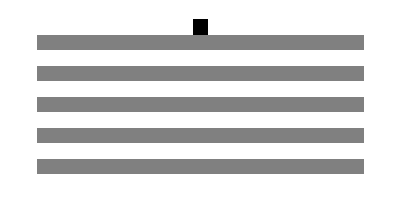
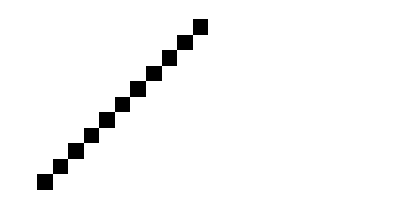
{-Graphics-5,-Graphics-6,-Graphics-7,-Graphics-8,-Graphics-9,-Graphics-10}

```mathematica
Table[Labeled[Quiet[ArrayPlot[Quiet[CAfromVector[BinaryRuleVector[i],2, 21, 10]]]], i],{i, 5, 10}]
```

### All Automata with Non-Boolean Initial Value

To explore a bit more, lets try to see the behavior of all Analog Cellular Automata (ACA) on non-binary inputs.
For example, if you expand the next cell, you see the result of every ACA run with an initial starting cell with a value of 1/2:
(Note: automata 179 converges to 0 quickly, but the Wolfram Language has trouble representing very small numbers and ends up giving an error.)

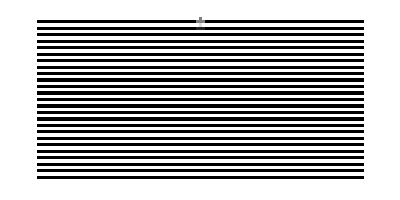
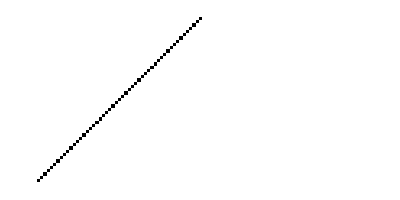
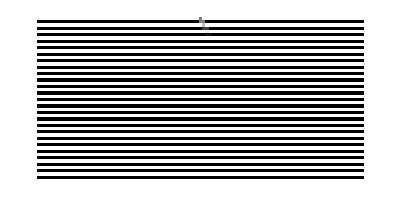
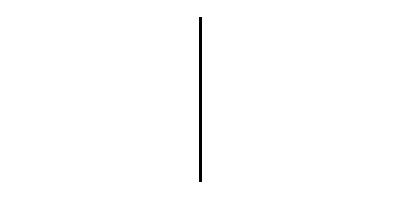
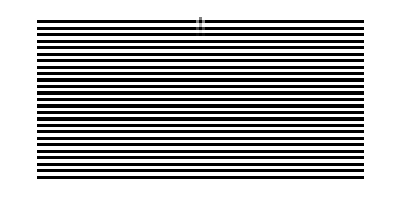
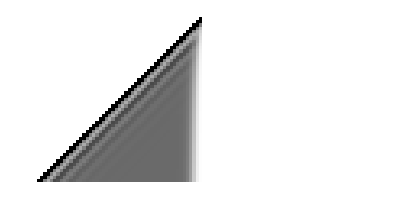
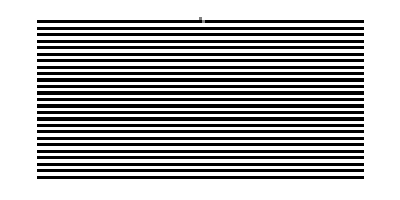
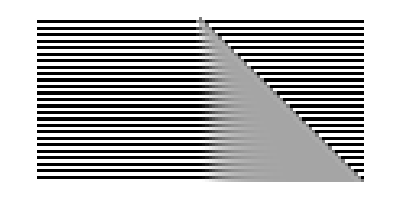
{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-6,-Graphics-7,-Graphics-8,-Graphics-9,-Graphics-10,-Graphics-11,-Graphics-12,-Graphics-13,-Graphics-14,-Graphics-15,-Graphics-16,-Graphics-17,-Graphics-18,-Graphics-19,-Graphics-20,-Graphics-21,-Graphics-22,-Graphics-23,-Graphics-24,-Graphics-25,-Graphics-26,-Graphics-27,-Graphics-28,-Graphics-29,-Graphics-30,-Graphics-31,-Graphics-32,-Graphics-33,-Graphics-34,-Graphics-35,-Graphics-36,-Graphics-37,-Graphics-38,-Graphics-39,-Graphics-40,-Graphics-41,-Graphics-42,-Graphics-43,-Graphics-44,-Graphics-45,-Graphics-46,-Graphics-47,-Graphics-48,-Graphics-49,-Graphics-50,-Graphics-51,-Graphics-52,-Graphics-53,-Graphics-54,-Graphics-55,-Graphics-56,-Graphics-57,-Graphics-58,-Graphics-59,-Graphics-60,-Graphics-61,-Graphics-62,-Graphics-63,-Graphics-64,-Graphics-65,-Graphics-66,-Graphics-67,-Graphics-68,-Graphics-69,-Graphics-70,-Graphics-71,-Graphics-72,-Graphics-73,-Graphics-74,-Graphics-75,-Graphics-76,-Graphics-77,-Graphics-78,-Graphics-79,-Graphics-80,-Graphics-81,-Graphics-82,-Graphics-83,-Graphics-84,-Graphics-85,-Graphics-86,-Graphics-87,-Graphics-88,-Graphics-89,-Graphics-90,-Graphics-91,-Graphics-92,-Graphics-93,-Graphics-94,-Graphics-95,-Graphics-96,-Graphics-97,-Graphics-98,-Graphics-99,-Graphics-100,-Graphics-101,-Graphics-102,-Graphics-103,-Graphics-104,-Graphics-105,-Graphics-106,-Graphics-107,-Graphics-108,-Graphics-109,-Graphics-110,-Graphics-111,-Graphics-112,-Graphics-113,-Graphics-114,-Graphics-115,-Graphics-116,-Graphics-117,-Graphics-118,-Graphics-119,-Graphics-120,-Graphics-121,-Graphics-122,-Graphics-123,-Graphics-124,-Graphics-125,-Graphics-126,-Graphics-127,-Graphics-128,-Graphics-129,-Graphics-130,-Graphics-131,-Graphics-132,-Graphics-133,-Graphics-134,-Graphics-135,-Graphics-136,-Graphics-137,-Graphics-138,-Graphics-139,-Graphics-140,-Graphics-141,-Graphics-142,-Graphics-143,-Graphics-144,-Graphics-145,-Graphics-146,-Graphics-147,-Graphics-148,-Graphics-149,-Graphics-150,-Graphics-151,-Graphics-152,-Graphics-153,-Graphics-154,-Graphics-155,-Graphics-156,-Graphics-157,-Graphics-158,-Graphics-159,-Graphics-160,-Graphics-161,-Graphics-162,-Graphics-163,-Graphics-164,-Graphics-165,-Graphics-166,-Graphics-167,-Graphics-168,-Graphics-169,-Graphics-170,-Graphics-171,-Graphics-172,-Graphics-173,-Graphics-174,-Graphics-175,-Graphics-176,-Graphics-177,-Graphics-178,ArrayPlot[CellularAutomaton[{{p$_,q$_,r$_}→(1-p$) (1-q$) (1-r$)+p$ (1-q$) (1-r$)+(1-p$) (1-q$) r$+p$ (1-q$) r$+p$ q$ r$},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},50]]179,-Graphics-180,-Graphics-181,-Graphics-182,-Graphics-183,-Graphics-184,-Graphics-185,-Graphics-186,-Graphics-187,-Graphics-188,-Graphics-189,-Graphics-190,-Graphics-191,-Graphics-192,-Graphics-193,-Graphics-194,-Graphics-195,-Graphics-196,-Graphics-197,-Graphics-198,-Graphics-199,-Graphics-200,-Graphics-201,-Graphics-202,-Graphics-203,-Graphics-204,-Graphics-205,-Graphics-206,-Graphics-207,-Graphics-208,-Graphics-209,-Graphics-210,-Graphics-211,-Graphics-212,-Graphics-213,-Graphics-214,-Graphics-215,-Graphics-216,-Graphics-217,-Graphics-218,-Graphics-219,-Graphics-220,-Graphics-221,-Graphics-222,-Graphics-223,-Graphics-224,-Graphics-225,-Graphics-226,-Graphics-227,-Graphics-228,-Graphics-229,-Graphics-230,-Graphics-231,-Graphics-232,-Graphics-233,-Graphics-234,-Graphics-235,-Graphics-236,-Graphics-237,-Graphics-238,-Graphics-239,-Graphics-240,-Graphics-241,-Graphics-242,-Graphics-243,-Graphics-244,-Graphics-245,-Graphics-246,-Graphics-247,-Graphics-248,-Graphics-249,-Graphics-250,-Graphics-251,-Graphics-252,-Graphics-253,-Graphics-254,-Graphics-255}

```mathematica
Table[Labeled[Quiet[ArrayPlot[CAfromVector[BinaryRuleVector[i],0.5]]], i],{i, 0, 255}]
```

Next, let’s try to find all the ACA that work for input values over 1. Most of these diverge to outside of the computable limit, so first I’ll define a function that iteratively searches for non-divergent automata:

```mathematica
(* Find all CA that avoid divergence by checking automata that have worked previously for higher and higher steps*)
FindWorkingCA:=Function[{init,maxt,bitThreshold},Module[{possibleInputs, t},
possibleInputs = Range[0, 255];
For[t=1,t<=maxt,t+=1,
possibleInputs = Pick[possibleInputs,
Table[
AllTrue[
Flatten[CAfromVector[
BinaryRuleVector[possibleInputs[[i]]],init,2*t+1,t
]],
BitLength[#]<=bitThreshold&
],
{i, Length[possibleInputs]}
]
]
];
possibleInputs
]]
```

And then I can use that to find, for example, all the ACA that do not diverge after 50 steps with an initial value of 2:

```mathematica
workingCA=FindWorkingCA[2, 50, 1024]
```

{0,2,4,7,8,10,12,13,15,16,19,21,23,24,27,29,31,32,34,36,39,40,42,44,48,50,51,53,55,56,58,63,64,66,68,69,71,72,74,76,77,79,80,83,85,87,88,93,95,96,98,100,104,106,108,112,114,119,120,122,127,128,130,132,136,138,140,144,151,152,159,160,162,164,168,170,171,172,173,175,176,178,179,183,184,186,187,189,191,192,194,196,200,201,202,203,204,205,207,208,215,216,217,219,221,223,224,226,228,229,231,232,234,235,236,237,238,239,240,241,242,243,245,247,248,249,250,251,252,253,254,255}

After looking through them all, I found this particularly interesting example: rule 77. It exhibits very different behavior for initial values of 0, 1, and 2.
(Note that the legend is not representative of the values that the automata actually computes, as I multiplied the value of every cell by 1/2 to scale it within the color function I’m using.)

```mathematica
Manipulate[ArrayPlot[0.5 * CAfromVector[BinaryRuleVector[77],n, 101, 50],ColorFunction->"TemperatureMap",ColorFunctionScaling->False,PlotLegends->BarLegend[{"TemperatureMap",{0,1}}], ImageSize->Large], {n, 0, 2}]
```

ArrayPlot::mat: 
   Argument 0.5 CAfromVector[BinaryRuleVector[77], 0, 101, 50] at position 1
     is not a list of lists.

I tried experimenting with a number of other values, but this graph was the most interesting I found. Perhaps another good place to explore would be if there are any interesting transitions as the input value changes, as, for the most part, I was only looking for interesting patterns in static input values.

## ACA with Non-Boolean Rule Vector

Although we defined ACA in terms of extrapolating ECA’s binary rules to non-binary inputs, we don’t actually need to use binary rules. That is, in the original derivation, for every rule, N need not be only 0 or 1, it can be anything. For a rule set of size eight, this means that ACA can use any eight-dimensional vector as a rule.
For example, here is random rule vector and it’s resulting cellular automaton:

```mathematica
RandomRuleVector := RandomReal[{0, 1}, 8];
```

```mathematica
ArrayPlot[CAfromVector[RandomRuleVector, 1, 51, 25]]
```

-Graphics-

Most of these don’t exhibit very much interesting behavior and eventually converge to a single number. We can search for more interesting automata and automata that don’t converge with a variety of methods. For example, this code searches through 100 random automata and outputs the 10 that showed the most complexity.  The way I’m defining complexity (which I call entropy in the code) is to minimize the number of repeating patterns of lengths 1 and 2 (and more if so desired), so that both convergence to a constant value (a pattern of length 1) and convergence to a simple alternating pattern (a pattern of length 2) are discouraged.

```mathematica
maxSearchT=10;  (* Maximum steps to search *)
maxT=10;  (* Maximum steps to display *)
numberOfRand = 1000;  (* Number of random vectors to search through *)
maxPatternLength = 2;  (* Maximum length of patterns to discourage *)

ListOfRandomRuleVectors = Table[RandomRuleVector, {i, numberOfRand}];

result = Table[CAfromVector[ListOfRandomRuleVectors[[i]], 1, 1 + 2 * maxSearchT, maxSearchT],{i, Length[ListOfRandomRuleVectors]}];

(* Method 1: Maximize Standard Deviation *)
(*
resultEntropy = Table[N[StandardDeviation[result[[i, maxSearchT]]]] + N[StandardDeviation[result[[i, maxSearchT - 1]]]], {i, 1, Length[result]}];
*)

(* Method 2: Minimize Repeating Patterns *)
PatternOfLengthN=Function[{n},Table[Total[Abs[Take[out, {-5, -1}, {1+n, -1}]- Take[out, {-5, -1}, {1, -1-n}]], 2], {out, result}]];
resultEntropy=Times@@@Transpose[Table[PatternOfLengthN[n], {n, maxPatternLength}]];


(* Sort and Output *)
sortedResult=Reverse[SortBy[Range[Length[resultEntropy]],resultEntropy[[#]]&]];

Table[Labeled[Quiet[ArrayPlot[CAfromVector[ListOfRandomRuleVectors[[sortedResult[[i]]]], 1, 2*maxT+1, maxT]]], sortedResult[[i]]],{i, Min[10, numberOfRand]}]
```

{-Graphics-555,-Graphics-392,-Graphics-643,-Graphics-600,-Graphics-248,-Graphics-148,-Graphics-126,-Graphics-660,-Graphics-285,-Graphics-633}

We can even pick random vectors outside of the range from 0 to 1, and there are some very interesting automata that arise (though most diverge). For example, here is a vector I found which is stable for about a bit over 1500 steps, but then diverges before 1600:

```mathematica
vector51 = {0.9347234831398135,-0.09439852555280281,0.9663267376484153,0.10130201454672605,0.9716205321003524,0.8008475726151447,0.9975397382122457,0.28201829843281434};
 ArrayPlot[CAfromVector[vector51, 1,2801, 1500], ImageSize->Full]
```

-Graphics-

### Python Implementation

To find interesting automata faster, I converted all my code into python and saved all the best vectors I found into a text file. The python code can test about 18 automata per second, and it can continuously search, finding as many as it can until I stop the program. It is faster because of significant optimizations in the definition of the rule function, because of vectorization through numpy, and because of the use of fixed precision numbers which take up much less RAM and don’t significantly impact the accuracy of the program (cell values outside of the float32 overflow limit almost certainly would just continue to diverge anyway).

The python code isn’t essential to understand; it does basically the exact same thing as the Wolfram code in this notebook. Here is an overview:
	First, it declares functions equivalent to functions built into the Wolfram Language.
	Next, it declares functions that I’ve used in this notebook, like RuleFunction and CAfromVector
	Then, it loops infinitely, creating and evaluating random automata
	The complexity of each automata is then determined, and if it is above a set threshold, the index is logged, the vector is logged, and the image of it is saved.

Here is the actual code:
(I’m not sure if it will actually run correctly here, I’m running it in a separate IDE. The code also saves to a specific file location on my computer which won’t exist on yours. The code also loops infinitely, continuously saving it’s last result to a file, so you need to abort it to stop it.)

import numpy as np
import matplotlib.pyplot as plt  # For Image Generation


# Implementing functions from the wolfram notebook
def Times(__iterable, start=1):
    o = start
    for element in __iterable:
        o *= element
    return o

def CenterArray(inLength):
    o = [0.] * inLength
    o[round(inLength / 2)] = 1 - 1e-5
    return o

def ArrayPlotToFile(table, title):  # Saves an image of the CA to a file
    plt.imshow(table, cmap='binary', interpolation='nearest')
    plt.title(title)
    plt.imsave("CellularAutomataImages/" + title + ".png", table)


def RuleFunc(r, n):
	# Computes the application of a rule (r) to a neighborhood (n)
    return r[0] * (1 - n[0]) * (1 - n[1]) * (1 - n[2]) + r[1] * (1 - n[0]) * (1 - n[1]) * n[2] + \
        r[2] * (1 - n[0]) * n[1] * (1 - n[2]) + r[3] * (1 - n[0]) * n[1] * n[2] + \
        r[4] * n[0] * (1 - n[1]) * (1 - n[2]) + r[5] * n[0] * (1 - n[1]) * n[2] + \
        r[6] * n[0] * n[1] * (1 - n[2]) + r[7] * n[0] * n[1] * n[2]

def CAfromVector(_rule, initial, steps):  # Runs the cellular automata 
    o = [initial]
    for _ in range(steps):
        o.append([RuleFunc(_rule, [o[-1][i-1]] + [o[-1][i]] + [o[-1][(i + 1) % len(initial)]]) for i in range(len(initial))])
    return o

def PatternOfLegnthN(n):
    return (abs(result[-5:-1, 1 + n:] - result[-5:-1, :-1 - n])).sum()


# Saving data to files
def logStringToFile(lineNumber, string, filePath):

    with open(filePath, 'r') as file:
        lines = file.readlines()
    if lineNumber > len(lines):
        lines.extend(['\n'] * (lineNumber - len(lines)))  # Add empty lines to reach the specified line
    lines[lineNumber - 1] = string + '\n'
    with open(filePath, 'w') as file:
        file.writelines(lines)

def writeNumberFound(n):
    with open("CellularAutomataLogs/CurrentIndex.txt", 'w') as file:
        file.write(str(n))

def readNumberFound():
    with open("CellularAutomataLogs/CurrentIndex.txt", 'r') as file:
        return int(file.read())


# Main part of the program
maxT = 50
entropyThreshold = 10  # Minimum Theshold entropy to be saved as an interesting vector

numberFound = readNumberFound()  # Reading saved progress for multiple sessions of the program
while True:
    rule = np.random.normal(0.5, 0.5, 8)  # Creating a random rule

    filename = '0' * (6 - len(str(numberFound))) + str(numberFound)
    ruleVectorName = str([format(x, '.16f') for x in rule]).replace("'", "")

    result = np.array(CellularAutomata(rule, CenterArray(maxT * 2 + 1), maxT))

    resultEntropy = Times([PatternOfLegnthN(n) for n in range(1, 3)])

    # Check for NAN, non-divergence, and if above threshold
    if 1e-16 <= resultEntropy <= 1e16 and not (result[-1] > 1e8).any() and resultEntropy > entropyThreshold:

        print(f'{filename}: | {ruleVectorName}')

        logStringToFile(numberFound, str(filename) + ' ' + ruleVectorName, "CellularAutomataLogs/IndexToVector.txt")
        logStringToFile(numberFound, ruleVectorName, "CellularAutomataLogs/InterestingVectors.txt")
        SaveArrayPlot(result, filename)

        numberFound += 1
        writeNumberFound(numberFound)  # Saving progress for multiple sessions of the program

Next, we need to extract the output of the python program, convert it into the correct format, and display it.
Out of the few hundred that it output on my computer, here are some of my most interesting vectors and their resulting ACA (scroll horizontally to see them all):
(Note: I hard-coded each vector, in case I accidentally overwrite the log file later, and so that they can be viewed without having the file on your computer.)

```mathematica
logPath="C:/Users/chris/PycharmProjects/Small Math Projects/Cellular Automata/CellularAutomataLogs/InterestingVectors.txt";
lastIndexPath="C:/Users/chris/PycharmProjects/Small Math Projects/Cellular Automata/CellularAutomataLogs/CurrentIndex.txt";

VectorFromFile=Function[{vectorIndex}, Reverse[ToExpression[StringJoin["{", StringTake[Import[logPath,"Lines"][[vectorIndex]], {2,-2}], "}"]]]];
lastVectorIndex :=ToExpression[Import[lastIndexPath,"Lines"][[1]]]-1


favoriteVectorIndices={5, 14, 24, 43, 70, 136};
(* favoriteVectors=VectorFromFile/@favoriteVectorIndices *)
favoriteVectors = {{0.2807171808301188,0.4557328758483759,-0.5930049930934539,-0.8071634360882323,0.3888735687029135,-0.3114075897289439,-0.5476384755338658,-0.8305588446023888},{-0.2099948272286002,-0.8318331946951691,1.9740113306145082,-0.3038251683760377,-0.7572455469340561,-0.7172840635197464,-0.4888717038656684,-0.4852456919157847},{1.029253935983736,0.8888811422531544,-0.4477585861720885,-0.403103244334353,0.5027241096629989,-0.3812947086051053,-0.6493457488721136,-0.9317164035610157},{0.7031871545694983,-0.3171610888423176,-0.9046366903640005,0.4351085497037068,0.1444307905328461,-0.9423656463228857,0.5263260906118812,1.0268370413377723},{0.342860951752864,1.1097053414047675,1.355883269159297,0.9186772076898599,0.9295750233304751,1.0937637699173628,0.9987765445348715,0.7447354797253269},{0.9793674085291821,0.2086216982653483,0.9026010297690132,0.3770080950758682,0.2274607955424446,-0.3585760244877866,0.821669964779238,0.9395472790229978}};

favoriteDivergentVectorIndices={17, 38, 52, 132, 133, 144, 213};
(* favoriteDivergentVectors=VectorFromFile/@favoriteDivergentVectorIndices *)
favoriteDivergentVectors = {{0.1169684341125803,0.1474161381779682,-0.3514870340333281,-0.6802088529923331,1.7598641030505187,-0.0886516237805488,0.3806197465620724,-0.143853400072368},{0.6662510582159569,0.7580217704627583,0.2852686835084621,0.768140632290855,-0.9360523288374403,-0.4013524265761204,0.5733843962632492,0.2208377154706782},{0.7569044093258923,0.7658759905707473,0.8540927531354607,0.1690020798486356,0.6045791099977424,-0.3627102701577515,-0.5992459987997154,-0.3442176464232889},{1.043148512467741,0.6539007350844716,0.3109479635081672,0.0359226364319544,1.199047506773769,0.6892431130181822,0.8389069001465991,0.7526218323682115},{1.060016507458517,0.78256605972764,0.1385801685318901,0.5701105410429992,0.3702793809103859,-0.0893158650918914,-0.5763808565250179,0.0652631901116003},{0.5573198871997853,1.5175110003644996,-0.1819132172544637,0.6922518321951936,0.2376283578309583,0.7933644865666936,0.0034832959780386,0.886083568964875},{0.2719815898224345,0.0442441683685778,1.0733075684449835,0.6507464792284631,0.303048857723151,-0.0865947971125974,1.6062487421355298,0.870934559311173}};
```

```mathematica
Table[Labeled[Quiet[ArrayPlot[CAfromVector[VectorFromFile[i], 1, 501, 250], ImageSize->Full]], i], {i, favoriteVectorIndices}]
```

{-Graphics-5,-Graphics-14,-Graphics-24,-Graphics-43,-Graphics-70,-Graphics-136}

Out of every ACA I’ve looked at, the following one has been my favorite and the most interesting to explore. It shows non-trivial behavior, it doesn’t seem to ever converge or diverge even when running it for 10,000 steps, it has seemingly random horizontal lines in the background that I don’t see a discernable pattern to, and it has fairly random behavior throughout.

```mathematica
V=favoriteDivergentVectors[[7]];
Manipulate[ArrayPlot[CAfromVector[V, n, 101,50], ImageSize->Large], {n, 0, 1}]
```

ArrayPlot::mat: 
   Argument CAfromVector[V, 0., 101, 50] at position 1 is not a list of lists.

ArrayPlot::mat: Argument CAfromVector[V,0.,101,50] at position 1 is not a list of lists.

Here is it extended to thousands of steps (as a PNG, because it was faster to create it with python):

```mathematica
Import["C:\\Users\\chris\\Documents\\array_plot_1.png"]
```

-Graphics-

## Nonlinear Rule Interpolation

Because of how we defined ACA rule functions, there are actually an infinite class of functions that can correspond to a single rule vector. For example, if we have the vector {N1, N2, N3, N4, N5, N6, N7, N8}, then any function that satisfy all of these conditions:
	f(0, 0, 0) = N1, f(0, 0, 1) = N2, f(0, 1, 0) = N3, f(0, 1, 1) = N4, f(1, 0, 0) = N5, f(1, 0, 1) = N6, f(1, 1, 0) = N7, f(1, 1, 1) = N8
will be a valid rule function.

We can make a few such alternate rule functions by applying an easing function (i.e., a function W such that W(0) = 0 and W(1) = 1) to it.

We can do this in one of two ways:
1. We can apply W to each input of the rule function.
2. We can change how we convert from a boolean function to an analog function. Instead of replacing the boolean ~x with the expression 1-x, we can replace ~x with any W(1-x).

For my exploration, I will use the second method, as it ensures that there is no preference to rules with inputs of zero rather than one (or vice versa). In other words, the second method will ensure that the average output over all possible neighborhoods for the rule vectors {1, 0, 0, 0, 0, 0, 0, 0} and {0, 0, 0, 0, 0, 0, 0, 1} are equal, which is not necessarily the case for the first method (e.g. W(x) = (1 - cos(pi * x / 2)).

### Implementation

```mathematica
NoEasingFunction=Function[{x},x];
CosineEasingFunction=Function[{x}, (1-Cos[Pi*x])/2];
SineEasingFunction=Function[{x}, Sin[Pi*x/2]];
SigmoidEasingFunction=Function[{steepness},Function[{x}, (LogisticSigmoid[steepness*(2*x-1)]-LogisticSigmoid[-steepness]) / (LogisticSigmoid[steepness]-LogisticSigmoid[-steepness])]];

transposedTuples = Transpose[Tuples[{0, 1}, 3]];

(* Given a rule vector (i.e., all the values of N, or the binary digits of a rule number), returns a function that implements it's analog analog *)
EasedRuleFunction := Function[{ruleVector, EasingFunction}, Function[{x, y, z}, 
Dot[
Reverse[
Times @@@ Map[
EasingFunction,
Transpose[((1 - transposedTuples)*(1 - {x, y, z})) + (transposedTuples * {x, y, z})],
{2}
]],ruleVector]]];

EasedCAfromVector[ruleVector_,EasingFunction_,initVal_:1,init_:101,t_:50]:= 
CellularAutomaton[
{{p_, q_, r_}->(EasedRuleFunction[ruleVector, EasingFunction])[p, q, r]},
initVal*(init/.{x_List:>x,x_:> CenterArray[x]}),t
]
```

Here is a visualization of all the easing functions I’ve implemented:

```mathematica
{
Labeled[Plot[NoEasingFunction[x], {x,0,1}], "No Easing Function"],
Labeled[Plot[CosineEasingFunction[x], {x,0,1}], "Cosine Easing"],
Labeled[Plot[SineEasingFunction[x], {x,0,1}], "Sine Easing"],
Labeled[Plot[SigmoidEasingFunction[2][x], {x,0,1}], "Minimal Sigmoid Easing"],
Labeled[Plot[SigmoidEasingFunction[5][x], {x,0,1}], "Severe Sigmoid Easing"]
}
```

{-Graphics-No Easing Function,-Graphics-Cosine Easing,-Graphics-Sine Easing,-Graphics-Minimal Sigmoid Easing,-Graphics-Severe Sigmoid Easing}

Now, lets see how these easing functions influence an automata. Here is a simple example of the rule 30 automata with an initial value of 0.6 using a variety of easing functions:

```mathematica
maxT=50;
initVal=0.6;
{
Labeled[ArrayPlot[EasedCAfromVector[BinaryRuleVector[30], NoEasingFunction, initVal, 2*maxT+1, maxT]], "No Easing Function"],
Labeled[ArrayPlot[EasedCAfromVector[BinaryRuleVector[30], CosineEasingFunction,initVal, 2*maxT+1, maxT]], "Cosine Easing"],
Labeled[ArrayPlot[EasedCAfromVector[BinaryRuleVector[30], SineEasingFunction, initVal, 2*maxT+1, maxT]], "Sine Easing"],
Labeled[ArrayPlot[EasedCAfromVector[BinaryRuleVector[30], SigmoidEasingFunction[2], initVal, 2*maxT+1, maxT]], "Minimal Sigmoid Easing"],
Labeled[ArrayPlot[EasedCAfromVector[BinaryRuleVector[30], SigmoidEasingFunction[5], initVal, 2*maxT+1, maxT]], "Severe Sigmoid Easing"]
}
```

{-Graphics-No Easing Function,-Graphics-Cosine Easing,-Graphics-Sine Easing,-Graphics-Minimal Sigmoid Easing,-Graphics-Severe Sigmoid Easing}

As you can see, No Easing function and the nearly linear Minimal Sigmoid Easing function make the output eventually converge. The Cosine and Severe Sigmoid easing functions tend to move inputs toward either 0 or 1, so we see the binary structure of the rule 30 ECA. Sine easing slightly prefers larger values, but I don’t know why it makes the interesting pattern that it does.

### Random Eased Automata

By pushing values towards 0 and 1, convergence happens less often, and for many easing functions (such as the ones I’ve implemented), extreme divergence is impossible. This means that the patterns gotten from random automata are often much more complex, and more automata tend to be computable. Here are 100 such automata:
(Note: Because divergence is now impossible, I am generated rule vectors from a normal distribution, which may go outside of [0, 1].)

```mathematica
maxT=50;  (* Maximum steps to display *)
numberOfRand = 100;  (* Number of random vectors to search through *)

ListOfRandomRuleVectors = Table[3 * RandomRuleVector - 1, {i, numberOfRand}];  (* Random vectors in range [=1, 2] *)

Table[Labeled[ArrayPlot[EasedCAfromVector[ListOfRandomRuleVectors[[i]], SigmoidEasingFunction[8], 1, 1 + 2 * maxT, maxT]], i],{i, numberOfRand}]
```

{-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-6,-Graphics-7,-Graphics-8,-Graphics-9,-Graphics-10,-Graphics-11,-Graphics-12,-Graphics-13,-Graphics-14,-Graphics-15,-Graphics-16,-Graphics-17,-Graphics-18,-Graphics-19,-Graphics-20,-Graphics-21,-Graphics-22,-Graphics-23,-Graphics-24,-Graphics-25,-Graphics-26,-Graphics-27,-Graphics-28,-Graphics-29,-Graphics-30,-Graphics-31,-Graphics-32,-Graphics-33,-Graphics-34,-Graphics-35,-Graphics-36,-Graphics-37,-Graphics-38,-Graphics-39,-Graphics-40,-Graphics-41,-Graphics-42,-Graphics-43,-Graphics-44,-Graphics-45,-Graphics-46,-Graphics-47,-Graphics-48,-Graphics-49,-Graphics-50,-Graphics-51,-Graphics-52,-Graphics-53,-Graphics-54,-Graphics-55,-Graphics-56,-Graphics-57,-Graphics-58,-Graphics-59,-Graphics-60,-Graphics-61,-Graphics-62,-Graphics-63,-Graphics-64,-Graphics-65,-Graphics-66,-Graphics-67,-Graphics-68,-Graphics-69,-Graphics-70,-Graphics-71,-Graphics-72,-Graphics-73,-Graphics-74,-Graphics-75,-Graphics-76,-Graphics-77,-Graphics-78,-Graphics-79,-Graphics-80,-Graphics-81,-Graphics-82,-Graphics-83,-Graphics-84,-Graphics-85,-Graphics-86,-Graphics-87,-Graphics-88,-Graphics-89,-Graphics-90,-Graphics-91,-Graphics-92,-Graphics-93,-Graphics-94,-Graphics-95,-Graphics-96,-Graphics-97,-Graphics-98,-Graphics-99,-Graphics-100}

Many of these automata

$Aborted

Just thought of something:
ACA similar to neural network? Use of training and backpropogation to acheive a specific output????

```mathematica
NumericalCAGrad[CAFunction_, EvalFunc_, ruleVector_, d_:0.01]:=
Table[
EvalFunc[CAFunction[
ruleVector+Table[If[j==i,d,0],{j,8}]
]], {i, 8}]-
EvalFunc[CAFunction[ruleVector]] / d;
```

```mathematica
d=0.01;

(* EvalFunc=StandardDeviation[#[[-1]]]&; *)
EvalFunc=N[Entropy[Flatten[#]]]&;

SpatialRandomnessTest
RandomnessTest=Function[{data}, Graph[Range[Length[data]],Table[UndirectedEdge[i,j],{i,Length[data]},{j,i+1,Length[data]}],EdgeWeight->Abs[Subtract[##]]&@@@Subsets[data,{2}

bestV={0.5, 0.5, 0.5, 0.5, 0.5, 0.5, 0.5, 0.5};
For[iter=1, iter<100, iter+=1, 
bestV=Table[If[el<=1-d, If[d<=el, el, d], 1-d], {el, bestV}];
grad=Normalize[NumericalCAGrad[EasedCAfromVector[#,SigmoidEasingFunction[8], 1, 11, 5]&, EvalFunc, bestV, d]];
bestV+=0.1*grad;
]
bestV
ArrayPlot[EasedCAfromVector[bestV, SigmoidEasingFunction[8], 1, 21, 10]]
```

```mathematica
result=EasedCAfromVector[RandomRuleVector, SineEasingFunction];
ArrayPlot[result]
```

-Graphics-

```mathematica
FindClusters
```

FindClusters

```mathematica
endResult=Take[result[[-1]], {1, 10}]
```

{-0.199148,-0.199206,-0.199725,-0.202134,-0.207169,-0.204539,-0.0812363,0.169846,0.0942752,0.244403}

```mathematica
1/(Flatten[Table[Abs[endResult[[i]]-endResult[[j]]], {i, Length[endResult]}, {j, i+1, Length[endResult]}]]/. {0.->0.001})

outputGraph=Graph[Flatten[Table[UndirectedEdge[i, j], {i, Length[endResult]}, {j, i+1, Length[endResult]}]], EdgeWeight->1/(Flatten[Table[Abs[endResult[[i]]-endResult[[j]]], {i, Length[endResult]}, {j, i+1, Length[endResult]}]]/. {0.->0.000001})]
```

{17264.8,1735.05,334.995,124.68,185.519,8.4809,2.71007,3.40804,2.25453,1928.89,341.623,125.587,187.534,8.47673,2.70964,3.40737,2.25424,415.15,134.333,207.73,8.43964,2.70584,3.40136,2.25161,198.594,415.771,8.27149,2.68832,3.37372,2.23946,380.196,7.94076,2.65241,3.31737,2.21449,8.11014,2.67105,3.34657,2.22746,3.98275,5.69763,3.07089,13.2326,13.4127,6.66101}

-Graphics-

```mathematica
minCut=FindMinimumCut[outputGraph]
g=outputGraph;
```

{36.5864,{{10},{1,2,3,4,5,6,7,8,9}}}

```mathematica
FindMinimumCut[g];
HighlightGraph[g,Map[Subgraph[g,#]&,Last[%]]]
```

-Graphics-